# Calculo de parejas poliamorosas

```mathematica
Libido[period_,phase_,t_]:=UnitStep[Sin[(2 π (t+phase))/period]];
CreatePopulation[n_,μ_,σ_,t_]:=Block[{periods,phases,libidoFunctions},
periods = RandomVariate[NormalDistribution[μ,σ],n];
phases = RandomReal[{0,30},n];
libidoFunctions = MapThread[Libido[#1,#2,t]&,{periods,phases}];
Total[libidoFunctions]
];
```

Este modelo define una función de Líbido la cual modela el deseo sexual de un individuo, que toma los valores de 0 si no está presente y 1 si está presente, con un periodo T. Cada individuo de una población tiene periodos  diferentes los cuales son generados por medio de una distrbución normal(μ,σ), y desfases aleatorios entre 1 y 30 días.

```mathematica
Manipulate[
Plot[
Libido[T,0,t],
{t,0,40}
],
{{T,15},1,30}
]
```

Una población de vínculos poliamorosos definen una función de líbido conjunta

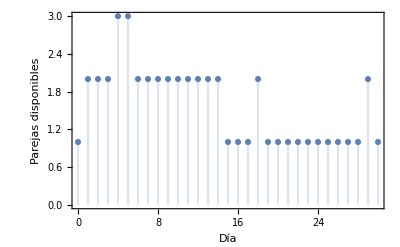

```mathematica
DiscretePlot[
Evaluate[CreatePopulation[3,28,4,tt]/.tt->t],
{t,0,30},
PlotRange->{{0,30},Automatic},
Frame->True,
FrameLabel->{"Día","Parejas disponibles"}
]
```

```mathematica
CreatePopulation[n_,μ_,σ_,t_]:=Block[{periods,phases,libidoFunctions},
periods = RandomVariate[NormalDistribution[μ,σ],n];
phases = RandomReal[{0,30},n];
libidoFunctions = MapThread[Libido[#1,#2,t]&,{periods,phases}];
Total[libidoFunctions]
];
TestMonth[n_,μ_,σ_]:=Block[{f,t},
f = CreatePopulation[n,μ,σ,t];
!MemberQ[Table[f,{t,0,31,1}],0]
];
CalculateProbability[l_]:=N[Count[l,True]/Length[l]];
ProbabilityOfSuccess[n_,μ_,σ_,samples_]:=CalculateProbability[Table[TestMonth[n,μ,σ],samples]];
```

La prueba estadística se hace la pregunta: ¿Se cumple que en el periodo de un mes siempre hay al menos un vínculo disponible?

```mathematica
probabilities = Table[{n,ProbabilityOfSuccess[n,28,4,10000]},{n,1,12}]
```

{{1,0.},{2,0.0338},{3,0.2588},{4,0.5049},{5,0.6996},{6,0.8235},{7,0.8937},{8,0.9374},{9,0.9704},{10,0.9818},{11,0.9893},{12,0.995}}

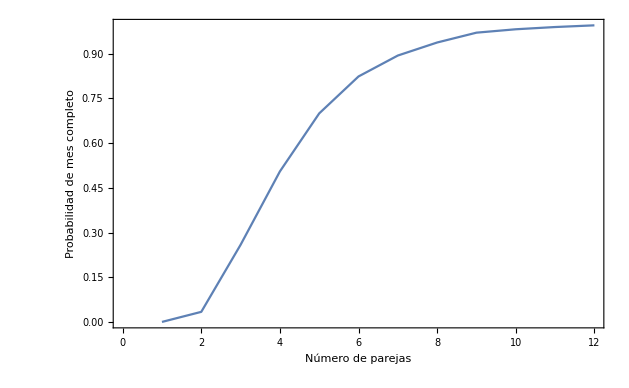

```mathematica
ListLinePlot[
probabilities,
Frame->True,
FrameLabel->{"Número de parejas","Probabilidad de mes completo"}
]
```